```mathematica
JosephusOperator[queue_]:=Delete[RotateLeft[queue,1],1]
```

```mathematica
JosephusRemaining[n_]:=First@NestWhile[JosephusOperator,Range[n],Length[#]>1&]
```

```mathematica
Print@@@NestWhileList[JosephusOperator,Range[5],Length[#]>1&];
```

12345

3451

513

35

3

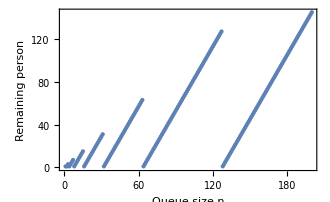

```mathematica
ListPlot[
Table[JosephusRemaining[n],{n,1,nmax=200}]
,Frame->True
,FrameLabel->{"Queue size n","Remaining person"}
,LabelStyle->{FontSize->16,FontFamily->"Times",Black}
,PlotRangePadding->0
]
```

```mathematica
JosephusOperatorII[queue_]:=Delete[RotateLeft[queue,1],1]/;Length[queue]>1
JosephusOperatorII[queue_]:=queue/;Length[queue]≤1
```

```mathematica
First@FixedPoint[JosephusOperatorII,Range[5]]
```

3